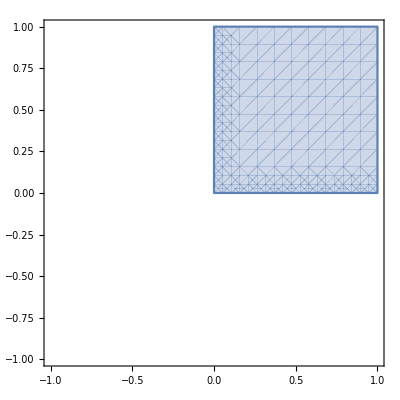

```mathematica
(*RAF AND BO: YOU CAN IGNORE THIS CELL-- SKIP TO THE NEXT ONE*)
(*TwoDConvexHull[y_]:=Interval[ {Min[y], Max[y]}];
GradSetx[f_, {x_, y_}] := {Limit[(f[{x+h, y}] - f[{x, y}]) / h, h -> 0, Direction->-1], Limit[(f[{x+h, y}] - f[{x, y}]) / h, h -> 0, Direction->1]}
GradSety[f_, {x_, y_}] := {Limit[(f[{x, y+h}] - f[{x, y}]) / h, h -> 0, Direction->-1], Limit[(f[{x, y+h}] - f[{x, y}]) / h, h -> 0, Direction->1]}
SubgradientSet[f_, x_, y_] := {TwoDConvexHull[GradSetx[f,{x, y}] ], TwoDConvexHull[GradSety[f,{x, y}] ] }
*)

(*RegionPlot[IntervalMemberQ[SubgradientSet[abstainLoss1, 0,0][[1]], x] &&IntervalMemberQ[SubgradientSet[abstainLoss1, 0,0][[2]], y], {x,-1,1}, {y,-1,1}]*)
```

```mathematica
(*Uncomment for abstain loss *)
(*reportset = {{-1,-1},{-1,1}, {1,1}, {1,-1}, {0,0} };
L1[{r1_, r2_}] := Max[0, 1 + r1,1 + r2]
L2[{r1_, r2_}] := Max[0, 1-r1, 1+ r2]
L3[{r1_, r2_}] := Max[0, 1-r1, 1-r2]
L4[{r1_, r2_}] := Max[0, 1+ r1, 1-r2]*)

(*Bo's epsilon loss*)
eps = 0.1;
L1[{r1_, r2_}]:=Max[r1+eps*r2,0]
L2[{r1_, r2_}]:=Max[r2+eps*r1,0]
L3[{r1_, r2_}]:=Max[1 + eps - r1 -eps*r2,0]
L4[{r1_, r2_}]:=Max[1 + eps - r2 -eps*r1,0]
reportset = {{0,0}, {1,1}, {1,-1}, {1,0}, {-1, 1}, {-1, -1}, {-1,0}, {0,1}, {0,-1}};

exL[{r1_,r2_}, {p1_, p2_, p3_, p4_}] := p1 L1[{r1, r2}] + p2 L2[{r1, r2}] + p3 L3[{r1, r2}] + p4 L4[{r1, r2}]

(*Manipulate[Plot3D[exL[{r1,r2}, {p1,p2,p3, 1-p1-p2-p3}], {r1,-1,1}, {r2,-1,1}, AxesLabel->{"x1", "x2"}], {p1,0,1}, {p2, 0,1}, {p3, 0, 1}]*)
```

```mathematica
Losses[{p1_, p2_, p3_}] :=  MapIndexed[exL[#1, {p1, p2 , p3,  1-p1-p2-p3}] &, reportset]
BR[{p1_, p2_, p3_}] := Simplify[Min[Losses[{p1, p2, p3}]], p1≥ 0&& p2 ≥ 0 && p3 ≥ 0&& p1 + p2 + p3 ≤ 1 ] (*Bayes Risk*)
ml[{p1_, p2_, p3_}] := BR[{p1, p2, p3}] /. Min -> List (* Parameterized version *)
MinLosses = ml[{p1, p2, p3}];
reducedreportset = DeleteCases[MapIndexed[If[MemberQ[MinLosses, Simplify[exL[#1, {p1, p2, p3, 1-p1-p2-p3}] ]], #1,Null ] &, reportset], Null] ;

reducedreportset
```

{{0,0},{1,1},{1,-1},{1,0},{-1,1},{0,1}}

```mathematica
levelsetboundaries = DeleteCases[DeleteCases[MapIndexed[Simplify[Solve[BR[{p1, p2, p3}] == #1[[1]] == #1[[2]] && 0 ≤ p1 ≤ 1 && 0 ≤ p2 ≤ 1 && 0 ≤ p3 ≤ 1 && p1 + p2 + p3 ≤ 1, {  p1,p2,p3}]][[1]] &, Subsets[MinLosses, {2}]], {}[[1]]] ,x_ /; NumericQ[p1/.x]];


(*Show[ParametricPlot3D[{p1, p2, p3} /. levelsetboundaries[[1]][[1]], {p2,0,1}, {p3,0,1}],
ParametricPlot3D[{p1, p2, p3} /. levelsetboundaries[[2]][[1]], {p1,0,1}, {p3,0,1}],
ParametricPlot3D[{p1, p2, p3} /. levelsetboundaries[[3]][[1]], {p1,0,1}, {p2,0,1}],
ParametricPlot3D[{p1, p2, p3} /. levelsetboundaries[[3]][[1]], {p2,0,1}, {p3,0,1}]
]*)

triples = MapIndexed[{p1, p2, p3} /. #1[[1]]&, levelsetboundaries];
paramvars = MapIndexed[DeleteCases[{p1, p2, p3} /. #1[[1]], x_ /; MatchQ[x, _ConditionalExpression]] &, levelsetboundaries];
condexps = MapIndexed[DeleteCases[{p1, p2, p3} /. #1[[1]], x_ /; Not[MatchQ[x, _ConditionalExpression]]] &, levelsetboundaries];
triples
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

{{ConditionalExpression[p3,0≤p2≤0.5&&1. p2+p3==0.5],p2,p3},{p1,ConditionalExpression[1.-2. p3,0≤p1<0.5&&p1≤p3≤0.0769231+0.846154 p1],p3},{ConditionalExpression[0.0909091-0.181818 p2+0.818182 p3,p2+1. p3≥0.5&&((0≤p3≤0.0769231&&p2≤0.5+4.5 p3)||(0.0769231<p3≤0.5&&p2+2. p3≤1.))],p2,p3},{ConditionalExpression[0.909091-1.81818 p2-0.818182 p3,0≤p2≤0.5&&0.153846 p2+p3≥0.0769231&&1. p2+p3≤0.5],p2,p3},{ConditionalExpression[1.-2. p2-2. p3,0≤p2≤0.5&&p3≥0&&0.153846 p2+p3≤0.0769231],p2,p3},{ConditionalExpression[0.909091-1.81818 p2-0.818182 p3,1. p2+p3≥0.5&&((0<p2≤0.0909091&&p3≤0.5+4.5 p2)||(0.0909091<p2<0.5&&2.22222 p2+p3≤1.11111))],p2,p3},{ConditionalExpression[0.0909091-0.181818 p2+0.818182 p3,0≤p3<0.340426&&0.039267+0.353403 p3≤p2&&p2+1. p3≤0.5],p2,p3},{ConditionalExpression[0.909091-1. p2-0.818182 p3,0.5 p2+p3≥0.5&&((0<p2≤0.5&&p3≤0.5)||(0.5<p2<0.846154&&1.22222 p2+p3≤1.11111))],p2,p3},{ConditionalExpression[0.,4.20539×10^-18<p2<0.5&&1. p2+p3==0.5],p2,p3},{ConditionalExpression[0.5-1. p2+4.5 p3,p3≥0&&((0≤p2≤0.123188&&0.153846 p2+p3≤0.0769231)||(0.123188<p2<0.136364&&4.4 p2+p3≤0.6))],p2,p3}}

```mathematica
plt[{x_, y_}, idx_] :=ParametricPlot3D[triples[[idx]], {x, 0, 1}, {y, 0, 1}, RegionFunction->Function[{p1, p2, p3}, p1 + p2 + p3 ≤ 1], PlotStyle->RandomColor[], MeshStyle->None]

Show[MapIndexed[plt[#1, #2]&, paramvars], Plot3D[1 - p1-p2, {p1, 0,1}, {p2, 0, 1}, PlotStyle-> Opacity[0], RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1]], PlotRange-> {{0,1}, {0,1}, {0,1}}, BoxRatios-> {1,1,1}, MaxRecursion-> 5]
(*MapIndexed[ParametricPlot3D[triples[[#1]], {paramvars[[#1]][[1]], 0, 1}, {paramvars[[#1]][[2]], 0, 1}]&, Length[triples]]*)

Show[MapIndexed[Plot3D[#1, {p2, 0,1}, {p3,0,1}, PlotStyle->RandomColor[], MeshStyle->None]&, condexps], Plot3D[1 - p1-p2, {p1, 0,1}, {p2, 0, 1}, PlotStyle-> Opacity[0], RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1]], PlotRange-> {{0,1}, {0,1}, {0,1}}, BoxRatios-> {1,1,1}]


(*bounds := DeleteDuplicates[DeleteCases[MapIndexed[Last@@@Simplify[Solve[#1[[1]] == #1[[2]] == BR[{p1, p2, p3}] && p1 ≥ 0 && p2 ≥ 0 && p3 ≥ 0 && p1 + p2 + p3 ≤ 1,   p3]]&, Subsets[MinLosses, {2}]], {}]]*)
```

-Graphics3D-

-Graphics3D-

```mathematica
Show[Plot3D[1 - p1-p2, {p1, 0,1}, {p2, 0, 1}, PlotStyle-> Opacity[0], RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1]], MapIndexed[Plot3D[#1, {p1,0,1}, {p2,0,1}, RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1], PlotStyle->{RandomColor[], Opacity[0.5]}]&, levelsetboundaries]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

Last::argt: Last called with 3 arguments; 1 or 2 arguments are expected.

Solve::svars: Equations may not give solutions for all "solve" variables.

Last::argt: Last called with 3 arguments; 1 or 2 arguments are expected.

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

Last::argt: Last called with 3 arguments; 1 or 2 arguments are expected.

General::stop: Further output of Last::argt will be suppressed during this calculation.

-Graphics3D-

```mathematica
(*Show[Plot3D[1 - p1-p2, {p1, 0,1}, {p2, 0, 1}, PlotStyle-> Opacity[0], RegionFunction->Function[{p1, p2}, p1 + p2 ≤ 1]],MapIndexed[RegionPlot3D[Reduce[First[#1] == Last[#1] == BR[{p1,p2,p3}] && 0≤ p1 ≤ 1 && 0≤ p2 ≤ 1 && 0 ≤ p3 ≤ 1 && p1 + p2 + p3 ≤ 1, {p1,p2, p3}], {p1,0,1}, {p2,0,1}, {p3,0,1}, PlotStyle->RandomColor[]] &, Subsets[MinLosses, {2}]], BoxRatios-> {1,1,1}]*)
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Reduce::ratnz will be suppressed during this calculation.

-Graphics3D-

```mathematica
Show[%193,Boxed->False]
```

-Graphics3D-

-Graphics3D-